```mathematica
(*Define the matrix of interest, R_lambda*)
R = {{-12,8,0,4},{lambda,-6-lambda,2,4},{0,2 lambda,-2-2 lambda,2},{0,0,0,0}}
```

{{-12,8,0,4},{lambda,-6-lambda,2,4},{0,2 lambda,-2-2 lambda,2},{0,0,0,0}}

```mathematica
MatrixForm[R]
```

(-12 | 8 | 0 | 4
lambda | -6-lambda | 2 | 4
0 | 2 lambda | -2-2 lambda | 2
0 | 0 | 0 | 0)

```mathematica
(*Double check it is row stochastic*)
Table[Sum[R[[i,j]],{j,1,4}],{i,1,4}]
```

{0,0,0,0}

```mathematica
(*Calculate the matrix transpose*)
(* this takes about a minute, and you can skip it because the next cell below has it cut-and-pasted *)
Assuming[lambda>0&&t>0,FullSimplify[{0,0,1,0}.(MatrixExp[R t].Transpose[{1,1,1,0}])]]
```

2 (-((4 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (-1+lambda (5+lambda)))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) (-2+lambda) (9+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] ((2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) (-1+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (2-2 lambda+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(4 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) (18+lambda (13+lambda)))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]^2)/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (-((2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (-1+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) (18+5 lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))))

```mathematica
(* cut-and-paste of previous cell*)
EPT2G[lambda_,t_]:=2 (-((4 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (-1+lambda (5+lambda)))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) (-2+lambda) (9+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] ((2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) (-1+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (2-2 lambda+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(4 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) (18+lambda (13+lambda)))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]^2)/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (-((2 ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]) (-1+lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1])/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]))+(ⅇ^(t Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]) (18+5 lambda))/(24 (18+lambda (13+lambda))+Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3] (216+4 lambda (19+lambda)+(20+3 lambda) Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]))))
```

```mathematica
(* no problem taking the series for small lambda; reproduces first line of (13) in manuscript *)
Assuming[t>0,Simplify[Series[EPT2G[lambda,t],{lambda,0,2}]]]
```

ⅇ^(-2 t)+1/4 ⅇ^(-6 t) (-1+ⅇ^(4 t) (1-4 t)) lambda+(ⅇ^(-12 t) (-8+25 ⅇ^(6 t) (5+24 t)+9 ⅇ^(10 t) (-13-20 t+200 t^2)) lambda^2)/3600+O[lambda]^3

```mathematica
(* but it doesn't like taking the series for large lambda *)
Assuming[t>0,Simplify[Series[EPT2G[lambda,t],{lambda,Infinity,1}]]]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 8+104 lambda+144 lambda^2+(2+38 lambda+108 lambda^2) #1+(3 lambda+20 lambda^2) #1^2+lambda^2 #1^3& for some values of lambda.

General::stop: Further output of Root::sbr will be suppressed during this calculation.

ⅇ^(-t lambda-10 t+(16 t)/lambda+O[1/lambda]^2) O[1/lambda]^2+(ⅇ^(-4 t)/4+(29 ⅇ^(-4 t))/(4 lambda)+O[1/lambda]^2)

```mathematica
(* so use Roots[] instead and take series/simplify one by one *)
Assuming[lambda>0,Roots[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) x+(20+3 lambda) x^2+x^3==0,x]]
```

x==1/3 (-20-3 lambda)-(2^(1/3) (-76-6 lambda-3 lambda^2))/(3 (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))+((-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(3 2^(1/3))||x==1/3 (-20-3 lambda)+((1+ⅈ √3) (-76-6 lambda-3 lambda^2))/(3 2^(2/3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))-((1-ⅈ √3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(6 2^(1/3))||x==1/3 (-20-3 lambda)+((1-ⅈ √3) (-76-6 lambda-3 lambda^2))/(3 2^(2/3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))-((1+ⅈ √3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(6 2^(1/3))

```mathematica
(*We do a series approximation for each root*)
(* series in large lambda for the first root above *)
Assuming[lambda>0,Simplify[Series[1/3 (-20-3 lambda)-(2^(1/3) (-76-6 lambda-3 lambda^2))/(3 (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))+((-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(3 2^(1/3)),{lambda,Infinity,4}]]]
```

-4+16/lambda^2-112/lambda^3+816/lambda^4+O[1/lambda]^5

```mathematica
(* give it a name/function for later *)
myroot1[lambda_]:=-4+16/lambda^2-112/lambda^3+816/lambda^4
```

```mathematica
(* series in large lambda for the second root above *)
Assuming[lambda>0,Simplify[Series[1/3 (-20-3 lambda)+((1+ⅈ √3) (-76-6 lambda-3 lambda^2))/(3 2^(2/3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))-((1-ⅈ √3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(6 2^(1/3)),{lambda,Infinity,4}]]]
```

-2 lambda-6-16/lambda-48/lambda^2+48/lambda^3+1616/lambda^4+O[1/lambda]^5

```mathematica
(* give it a name/function for later *)
myroot2[lambda_]:=-2 lambda-6-16/lambda-48/lambda^2+48/lambda^3+1616/lambda^4
```

```mathematica
(* series in large lambda for the third root above *)
Assuming[lambda>0,Simplify[Series[1/3 (-20-3 lambda)+((1-ⅈ √3) (-76-6 lambda-3 lambda^2))/(3 2^(2/3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))-((1+ⅈ √3) (-448-252 lambda+90 lambda^2+√(4 (-76-6 lambda-3 lambda^2)^3+(-448-252 lambda+90 lambda^2)^2))^(1/3))/(6 2^(1/3)),{lambda,Infinity,4}]]]
```

-lambda-10+16/lambda+32/lambda^2+64/lambda^3-2432/lambda^4+O[1/lambda]^5

```mathematica
(* give it a name/function for later *)
myroot3[lambda_]:=-lambda-10+16/lambda+32/lambda^2+64/lambda^3-2432/lambda^4
```

```mathematica
(* give the polynomial a name/function for convenience too *)
theploynomial[lambda_,x_]:=144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) x+(20+3 lambda) x^2+x^3
```

100

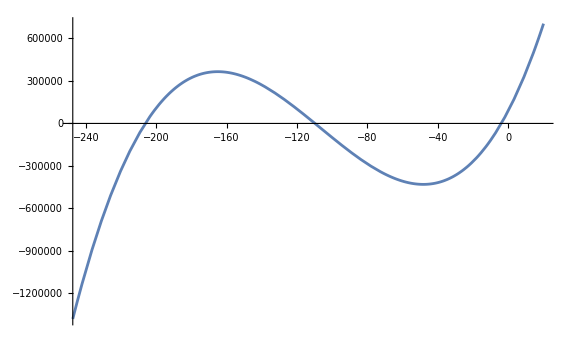

```mathematica
(* plot of the polynomial and your series for its three roots; note they are not in the same order as above *)
(* specify whatever value of lambda you want: *)
testlambda=100
Plot[theploynomial[testlambda,x],{x,1.2*myroot2[testlambda],testlambda/5},AxesOrigin->{1.2*myroot2[testlambda],0},GridLines->{{{myroot2[testlambda],Thick},{myroot3[testlambda],Thick},{myroot1[testlambda],Thick}},{}},ImageSize->Large]
Clear[testlambda]
```

10

200

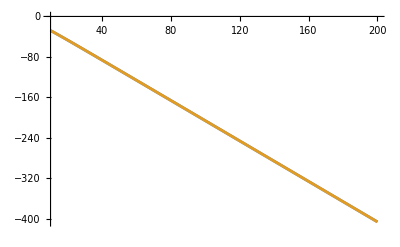

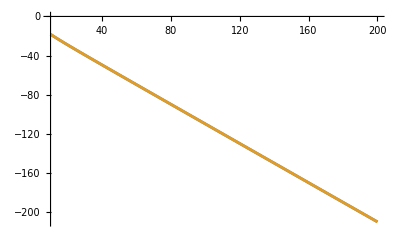

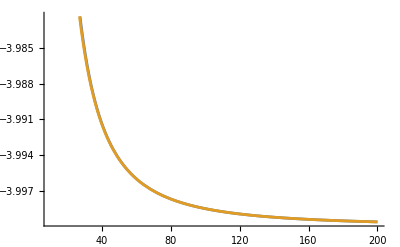

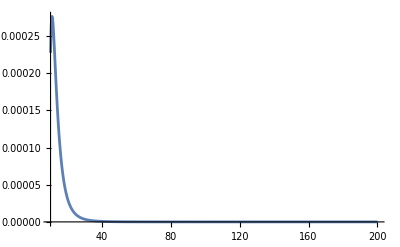

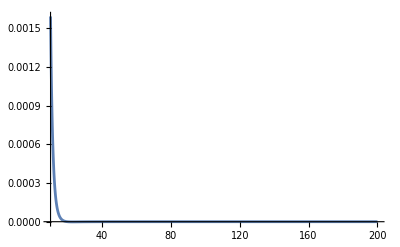

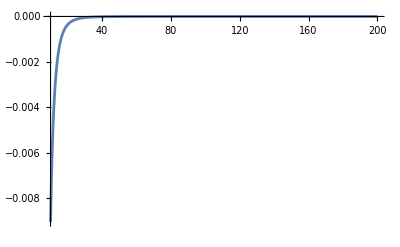

```mathematica
(* compare your series over a range of lambda with the outputs of Root[] as in myEPT2G[lambda,t] *) 
lowerlambda = 10
upperlambda=200
Plot[{myroot2[lambda],Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]},{lambda,lowerlambda,upperlambda}]
Plot[{myroot3[lambda],Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]},{lambda,lowerlambda,upperlambda}]
Plot[{myroot1[lambda],Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]},{lambda,lowerlambda,upperlambda}]
(* those line up very closely at this scale, so plot relative errors: *)
Plot[myroot2[lambda]/Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,1]-1,{lambda,lowerlambda,upperlambda},PlotRange->All]
Plot[myroot3[lambda]/Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,2]-1,{lambda,lowerlambda,upperlambda},PlotRange->All]
Plot[myroot1[lambda]/Root[144+104 lambda+8 lambda^2+(108+38 lambda+2 lambda^2) #1+(20+3 lambda) #1^2+#1^3&,3]-1,{lambda,lowerlambda,upperlambda},PlotRange->All]
Clear[lowerlambda,upperlambda]
```

```mathematica
(* now define a series version of EPT2G[lambda,t] using these results, *)
(* i.e. by putting your root series in for the corresponding instance of Root[] *)
myEPT2G231[lambda_,t_]:=2 (-((4 ⅇ^(t myroot2[lambda]) (-1+lambda (5+lambda)))/(24 (18+lambda (13+lambda))+myroot2[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot2[lambda])))+(2 ⅇ^(t myroot3[lambda]) (-2+lambda) (9+lambda))/(24 (18+lambda (13+lambda))+myroot3[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot3[lambda]))+myroot3[lambda] ((2 ⅇ^(t myroot3[lambda]) (-1+lambda))/(24 (18+lambda (13+lambda))+myroot3[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot3[lambda]))+(ⅇ^(t myroot2[lambda]) (2-2 lambda+myroot1[lambda]))/(24 (18+lambda (13+lambda))+myroot2[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot2[lambda])))+(4 ⅇ^(t myroot1[lambda]) (18+lambda (13+lambda)))/(24 (18+lambda (13+lambda))+myroot1[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot1[lambda]))+(ⅇ^(t myroot1[lambda]) myroot1[lambda]^2)/(24 (18+lambda (13+lambda))+myroot1[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot1[lambda]))+myroot1[lambda] (-((2 ⅇ^(t myroot2[lambda]) (-1+lambda))/(24 (18+lambda (13+lambda))+myroot2[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot2[lambda])))+(ⅇ^(t myroot3[lambda]) myroot2[lambda])/(24 (18+lambda (13+lambda))+myroot3[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot3[lambda]))+(ⅇ^(t myroot1[lambda]) (18+5 lambda))/(24 (18+lambda (13+lambda))+myroot1[lambda] (216+4 lambda (19+lambda)+(20+3 lambda) myroot1[lambda]))))
```

```mathematica
N[myEPT2G231[100,1]]
```

0.0185313

2

100

1000

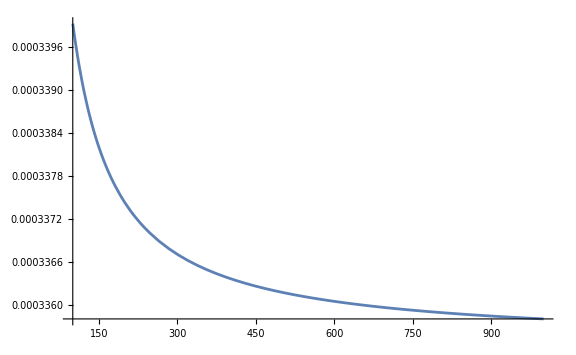

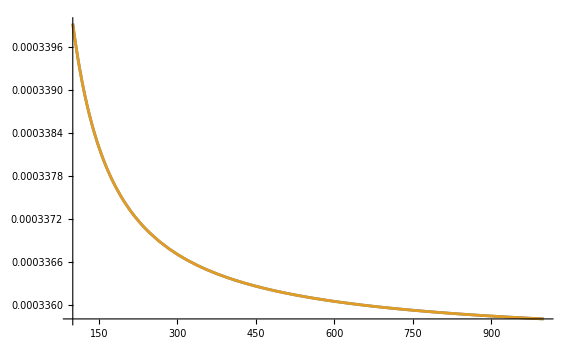

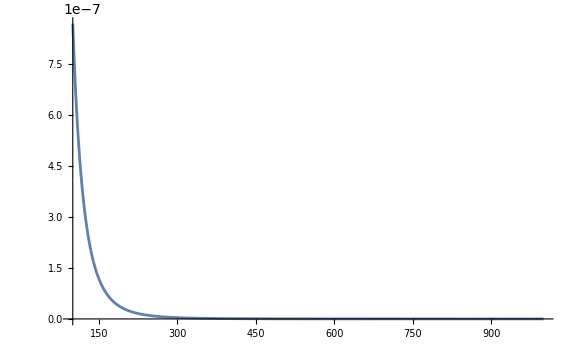

```mathematica
(* compare myEPT2G231[lambda,t] to EPT2G[lambda,t], both absolutely and realtively *)
(* here now for a given t over a range of lambda; specify whatever you want: *)
(* except your series version doesn't like small lambda; ok with 5 or bigger it seems *)
testt=2
lowerlambda = 100
upperlambda=1000
Plot[EPT2G[lambda,testt],{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Plot[{myEPT2G231[lambda,testt],EPT2G[lambda,testt]},{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Plot[myEPT2G231[lambda,testt]/EPT2G[lambda,testt]-1,{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Clear[testt,lowerlambda,upperlambda]
(* overall looks pretty good *)
```

```mathematica
(* now try the series for the second line of (13) in the manuscript *)
Assuming[t>0,FullSimplify[Series[myEPT2G231[lambda,t],{lambda,Infinity,3}]]]
```

ⅇ^(-t lambda-10 t+(16 t)/lambda+O[1/lambda]^2) (-4/lambda+O[1/lambda]^2)+ⅇ^(-2 t lambda-6 t-(16 t)/lambda+O[1/lambda]^2) (-2/lambda+O[1/lambda]^2)+ⅇ^(-2 t lambda-6 t-(16 t)/lambda-(48 t)/lambda^2+(48 t)/lambda^3+O[1/lambda]^4) (1/lambda+15/lambda^2-45/lambda^3+O[1/lambda]^4)+ⅇ^(-t lambda-10 t+(16 t)/lambda+(32 t)/lambda^2+(64 t)/lambda^3+O[1/lambda]^4) (4/lambda-28/lambda^2+200/lambda^3+O[1/lambda]^4)+(ⅇ^(-4 t)+ⅇ^(-4 t)/lambda+(ⅇ^(-4 t) (3+16 t))/lambda^2-(ⅇ^(-4 t) (43+96 t))/lambda^3+O[1/lambda]^4)

```mathematica
(* give it a name, keeping up to order 1/lambda^3 to be safe, though I guess you could keep 1/lambda^4 *)
(* also nothing stoping you from keeping more than 1/lambda^4 in your root series above, and more then here too *)
myEPT2Gseries[lambda_,t_]:=ⅇ^(-4 t)+ⅇ^(-4 t)/lambda+(ⅇ^(-4 t) (3+16 t))/lambda^2-(ⅇ^(-4 t) (43+96 t))/lambda^3
```

10

5

100

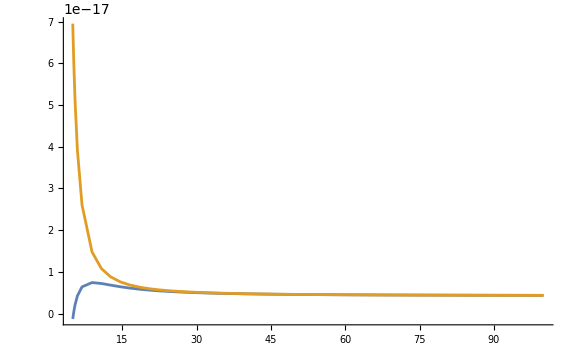

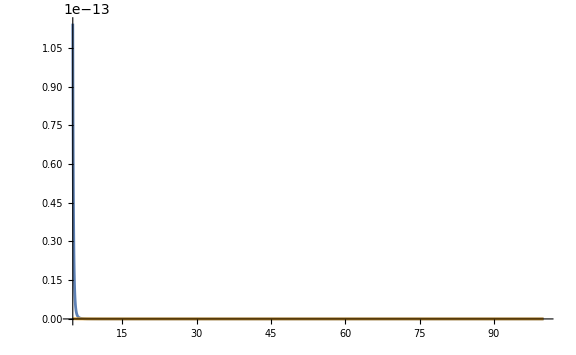

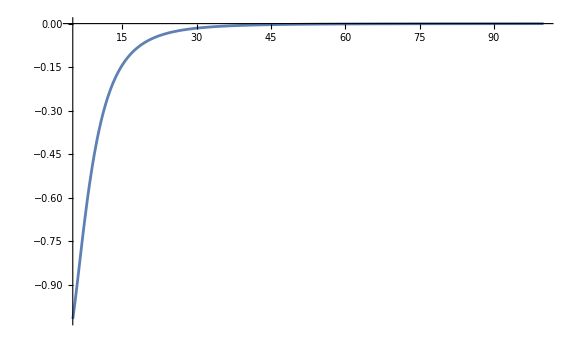

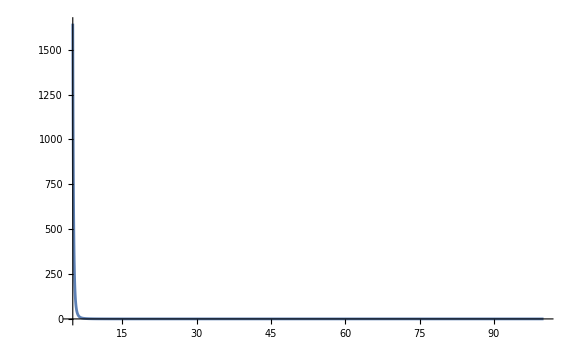

```mathematica
(* same plots as above, and it looks like myEPT2Gseries[lambda,t] is really not worse than myEPT2G231[lambda,t] *)
testt=10
lowerlambda = 5
upperlambda=100
Plot[{myEPT2Gseries[lambda,testt],EPT2G[lambda,testt]},{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Plot[{myEPT2G231[lambda,testt],EPT2G[lambda,testt]},{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Plot[myEPT2Gseries[lambda,testt]/EPT2G[lambda,testt]-1,{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Plot[myEPT2G231[lambda,testt]/EPT2G[lambda,testt]-1,{lambda,lowerlambda,upperlambda},ImageSize->Large,AxesOrigin->{lowerlambda,Automatic},PlotRange->All]
Clear[testt,lowerlambda,upperlambda]
```